# Spacelike collinear 5-point examples

Seed diagnostic at In[1]-In[5]. Full 7/8-propagator scan at In[6] (optional). Polynomial study at In[14].

Kernel "Local" (Evaluation > Notebook's Kernel). On open, init prints a reminder only. Restart Kernel once manually, then run In[1] onward. Do not put RestartKernel in auto-run init cells.

```mathematica
Print["HRF notebook loaded. Before In[1], use Evaluation > Restart Kernel once (manual)."];
```

Run the seed diagram diagnostic (In[1]-In[5]) first. The full 7/8-propagator topology scan is disabled until the seed case finds a hidden region with a single generator.

## Seed diagram diagnostic (run first)

Fast seed-only workflow (matches working binomial Ex03): polynomial f_k kin-normalized and Mandelstam-linear, SingleProduct generator g = product of all simultaneously admissible f_k. In[4] should show SafeSingleProductSetCount >= 1 before In[5].

```mathematica
$HRFEx03RunFullTopologyScanQ=False;$HRFEx03UsePolynomialFactorsQ=True;$HRFEx03ObstructionProgressQ=True;$HRFExampleVerbose=False;$HRFVerboseScaling=False;$HRFScalingReport=False;$HRFQuietReports=False;$HRFFindObstructionsStopOnFirstAdmissibleQ=False;$HRFCandidateGeneratorSetLimit=64;$HRFPolynomialMaxMonomials=30;$HRFPolynomialRequireKinematicDomainQ=False;$HRFUseGeneratorPhysicsFilterQ=True;Get[FileNameJoin[{NotebookDirectory[],"HiddenRegionFinder.wl"}]];Get[FileNameJoin[{NotebookDirectory[],"HRF_Example03CollinearCore.wl"}]];Get[FileNameJoin[{NotebookDirectory[],"HRF_PolynomialCancellationFactors.wl"}]];hrfInstallPolynomialCancellationPatch[];Get[FileNameJoin[{NotebookDirectory[],"HRF_Example03SeedStudy.wl"}]];hrfEx03SeedStudyLoad[];
```

[loaded] generator physics filter (kin pairing + sector quotient).

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[patch loaded] Obstruction reporting: F_0^restricted - Obstruction = F_SL; Obstruction + F_SL = F_0^restricted.

[loaded] Example 01 common reporting helpers.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[loaded] polynomial-factor reporting helpers.

[loaded] HRF_WideAngleBoundaryDiagnostic.wl — try hrfWideAngleBoundaryDiagnostic["HyperCrownX11"]

[Example 03 core] seed vars=6  ThreeLoopVertex vars=9  (no graph/boundary scans).

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[Example 03 seed] loaded. Evaluate hrfEx03SeedRouteComparison[], hrfEx03SeedFivePointRouteStudy[], hrfEx03RunSeedObstruction[].

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[loaded] five-point reporting helpers.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

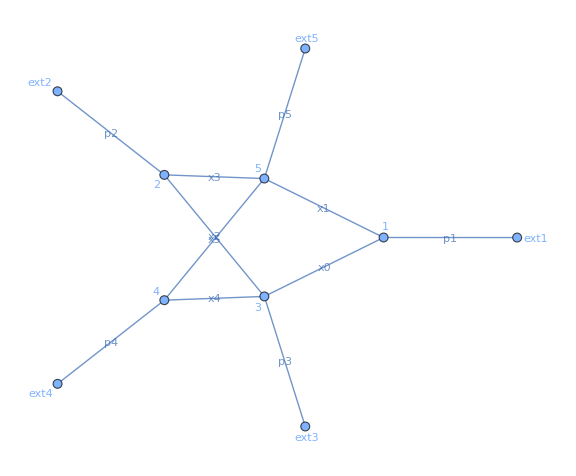

```mathematica
drawGraphFromPySecDecInput[seedInternalLines,seedExternalLines]
```

```mathematica
hrfEx03SeedFactorTable[]
```

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

```mathematica
hrfEx03SeedGeneratorAudit[]
```

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

<|GeneratorMode→SingleProduct,UseExtendedFactors→False,RelaxSingleProductDegreeQ→False,SkipPDFFindInstanceQ→False,SafeFactorCount→2,GeneratorEligibleFactorCount→2,BinomialEligibleFactorCount→2,SingleProductGeneratorFactorCount→2,SimultaneouslyAdmissibleLegacyBinomialPoolQ→True,SafeSingleProductSets→{{-x1 x2 x4-x1 x3 x4-x x0 x2 x5-x x0 x3 x5+x1 x2 x4 z+x x0 x2 x5 z}},SafeSingleProductSetCount→1,SimultaneouslyAdmissibleGeneratorPoolQ→True,FullProductDegreeAdmissibleQ→True,NonlinearSafeFactors→{}|>

Route comparison: canonical f_k (one row per class), all eligible pair products with rejection reasons, obstruction trial stages. Seed5pt only â.80.94 ThreeLoopVertex is at In[5c] and In[14].

```mathematica
Ex03RouteComparison=hrfEx03SeedRouteComparison[];Ex03RouteComparison["Summary"]
```

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[Example 03] finding cancellation factors (6 vars, maxSize Automatic)...

[Example 03] 2 cancellation factors; building generator trials (mode SingleProduct)...

[Example 03] obstruction search: 1 generator trials (cap 64); max obstruction size computed per set from |F| - sum|monomials(g_i)|

[Example 03] trial 1/1 (|gens|=1, kin-free=0)

08:37:36  [coverage routine] findCoverageLPScaling FAST entered vars=6 maxAbs=5 bruteBox=46655

08:37:36  [coverage candidate generation] method=nullspace vars=6 maxAbs=5 monomialRows=4 homogeneityRank=2 nullspaceDim=4 coeffBox=14640

08:37:36  [coverage candidates] method=FSLNullspaceCoefficients candidateCount=797 exhaustiveQ=True

08:37:36  [coverage candidate testing start] candidates=797

08:37:36  [coverage candidate testing end] accepted=99

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

<|RootCauseSummary→{Both routes select the same 2 canonical f_k after cleanup; polynomial pool is a superset for this seed.,Raw (1-z)-shelled and core f_k are one canonical class after Factor stripping of non-x_i shells.},Counts→<|LegacyBinomialSafe→2,PolynomialSafeCanonical→2,BinomialRouteSelected→2,PolynomialRouteSelected→2,PolynomialAdmissiblePairs→1|>,HiddenRegionQ→<|PolynomialObstructionScan→True|>,ColumnGuide→{CanonicalFactorTable / FactorTable: one row per canonical f_k (all safe-pool classes).,ChosenForGeneratorQ: picked by SingleProduct resolver on polynomial pool (not all admissible pairs).,GeneratorPairAuditTable: kin-prefiltered pairs g=f1*f2 (no kin-square / shared kin var); Factor1 has lower x-degree.,ObstructionTrialTable: after generator fixed, SL decomposition, sector PDF, scaling / HiddenRegionQ.,Selected in route comparison = resolver choice for that safe pool, not the only admissible generator.}|>

```mathematica
Ex03RouteComparison["CanonicalFactorTable"]
```

```mathematica
Ex03RouteComparison["GeneratorPairAuditTable"]
```

```mathematica
Ex03RouteComparison["GeneratorSelectionTable"]
```

Optional: every raw harvest variant.

```mathematica
Ex03RouteComparison["FactorTableVerbose"]
```

```mathematica
Ex03SeedObstruction=hrfEx03RunSeedObstruction[];KeyTake[Ex03SeedObstruction,{"HiddenRegionQ","Generators","AttemptSummary"}]
```

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[Example 03] finding cancellation factors (6 vars, maxSize Automatic)...

[Example 03] 2 cancellation factors; building generator trials (mode SingleProduct)...

[Example 03] obstruction search: 1 generator trials (cap 64); max obstruction size computed per set from |F| - sum|monomials(g_i)|

[Example 03] trial 1/1 (|gens|=1, kin-free=0)

08:37:38  [coverage routine] findCoverageLPScaling FAST entered vars=6 maxAbs=5 bruteBox=46655

08:37:38  [coverage candidate generation] method=nullspace vars=6 maxAbs=5 monomialRows=4 homogeneityRank=2 nullspaceDim=4 coeffBox=14640

08:37:38  [coverage candidates] method=FSLNullspaceCoefficients candidateCount=797 exhaustiveQ=True

08:37:38  [coverage candidate testing start] candidates=797

08:37:38  [coverage candidate testing end] accepted=99

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[Example 03 seed] seed obstruction: Safe=2 eligible=2 simultaneous=True SingleProductSets=1 HiddenRegionQ=True (ThreeLoopVertex: evaluate In[5c] or In[14a]-[14b])

<|HiddenRegionQ→True,Generators→{(x1 x4+x x0 x5) (-x2-x3+x2 z)},AttemptSummary→<|TrialCount→1,CandidateGeneratorCount→1,PerGeneratorAdmissibleCount→1,CandidateUnionPDFAdmissibleCount→1,ObstructionFindInstanceCount→1,AdmissibleSLSectorCount→1,ValidObstructionCount→1,HiddenRegionWithValidScalingCount→1,ScalingEvaluatedOnValidTrialsQ→True,GeneratorCountHistogram→<|1→1|>,StopOnFirstValidObstructionQ→False,StoppedEarlyOnValidObstructionQ→False|>|>

```mathematica
Ex03SeedObstruction["GeneratorPairAuditTable"]
```

```mathematica
Ex03SeedObstruction["ObstructionTrialTable"]
```

## Seed5pt vs ThreeLoopVertex (generator audit)

Both topologies: canonical f_k table (Topology column), pair audit, binomial vs polynomial resolver. Vertex obstruction skipped by default.

```mathematica
Ex03FivePointRoutes=hrfEx03SeedFivePointRouteStudy[];Ex03FivePointRoutes["GeneratorSelectionTable"];Ex03FivePointRoutes["CanonicalFactorTable"];Ex03FivePointRoutes["GeneratorPairAuditTable"]
```

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[Example 03] finding cancellation factors (6 vars, maxSize Automatic)...

[Example 03] 2 cancellation factors; building generator trials (mode SingleProduct)...

[Example 03] obstruction search: 1 generator trials (cap 64); max obstruction size computed per set from |F| - sum|monomials(g_i)|

[Example 03] trial 1/1 (|gens|=1, kin-free=0)

08:37:53  [coverage routine] findCoverageLPScaling FAST entered vars=6 maxAbs=5 bruteBox=46655

08:37:53  [coverage candidate generation] method=nullspace vars=6 maxAbs=5 monomialRows=4 homogeneityRank=2 nullspaceDim=4 coeffBox=14640

08:37:53  [coverage candidates] method=FSLNullspaceCoefficients candidateCount=797 exhaustiveQ=True

08:37:53  [coverage candidate testing start] candidates=797

08:37:53  [coverage candidate testing end] accepted=99

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

```mathematica
Ex03FivePointRoutes["ThreeLoopVertex"]["NonBinomialGeneratorSelectedQ"];Ex03FivePointRoutes["HiddenRegionQ"]
```

<|Seed5pt→True,ThreeLoopVertex→Missing[Skipped]|>

## Full 7/8-propagator scan (disabled until seed OK)

Optional and slow (~1-3 h). Only run after In[5] reports HiddenRegionQ=True with a single generator. This reloads the full Example 03 driver with $HRFEx03RunFullTopologyScanQ=True.

```mathematica
$HRFEx03RunFullTopologyScanQ=True;$HRFEx03UsePolynomialFactorsQ=True;$HRFEx03ObstructionProgressQ=True;$HRFEx03SevenPropBoundaryZeroVars={x6};$HRFEx03RunEightPropBoundaryScanQ=False;$HRFExampleVerbose=False;$HRFVerboseScaling=False;$HRFScalingReport=False;$HRFQuietReports=False;$HRFFindObstructionsStopOnFirstAdmissibleQ=True;$HRFCandidateGeneratorSetLimit=64;$HRFPolynomialMaxMonomials=12;$HRFPolynomialRequireKinematicDomainQ=False;Get[FileNameJoin[{NotebookDirectory[],"HiddenRegionFinder.wl"}]];Get[FileNameJoin[{NotebookDirectory[],"03_FivePoint_Spacelike_Collinear.wl"}]];
```

Requires In[6] (full load). These tables are independent of the polynomial obstruction cells below.

```mathematica
InterpretationBox[StyleBox["TopologyHiddenRegionTable2Loop7Prop",ShowStringCharacters->True],TopologyHiddenRegionTable2Loop7Prop,Editable->False]
```

```mathematica
InterpretationBox[StyleBox["TopologyRegionScalingTable2Loop7Prop",ShowStringCharacters->True],TopologyRegionScalingTable2Loop7Prop,Editable->False]
```

```mathematica
InterpretationBox[StyleBox["TopologyScalingCoverageTable2Loop7Prop",ShowStringCharacters->True],TopologyScalingCoverageTable2Loop7Prop,Editable->False]
```

## Eight-propagator summary tables (optional)

```mathematica
InterpretationBox[StyleBox["TopologyHiddenRegionTable2Loop8Prop",ShowStringCharacters->True],TopologyHiddenRegionTable2Loop8Prop,Editable->False]
```

```mathematica
InterpretationBox[StyleBox["TopologyRegionScalingTable2Loop8Prop",ShowStringCharacters->True],TopologyRegionScalingTable2Loop8Prop,Editable->False]
```

```mathematica
InterpretationBox[StyleBox["TopologyScalingCoverageTable2Loop8Prop",ShowStringCharacters->True],TopologyScalingCoverageTable2Loop8Prop,Editable->False]
```

## Export tables (optional)

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"TopologyHiddenRegionRows2Loop7Prop.csv"}],Normal[TopologyHiddenRegionTable2Loop7Prop]];Export[FileNameJoin[{NotebookDirectory[],"TopologyHiddenRegionRows2Loop8Prop.csv"}],Normal[TopologyHiddenRegionTable2Loop8Prop]];
```

## Five-point polynomial study (Seed5pt vs ThreeLoopVertex, duplicate of In[5c])

Same as In[5c] if already evaluated. Vertex obstruction scan skipped by default; set SkipVertexObstructionScans -> False for full vertex HiddenRegionQ (slow).

```mathematica
Ex03FivePointRoutes=hrfEx03SeedFivePointRouteStudy[];Ex03FivePointRoutes["CanonicalFactorTable"]
```

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[Example 03] finding cancellation factors (6 vars, maxSize Automatic)...

[Example 03] 2 cancellation factors; building generator trials (mode SingleProduct)...

[Example 03] obstruction search: 1 generator trials (cap 64); max obstruction size computed per set from |F| - sum|monomials(g_i)|

[Example 03] trial 1/1 (|gens|=1, kin-free=0)

08:38:34  [coverage routine] findCoverageLPScaling FAST entered vars=6 maxAbs=5 bruteBox=46655

08:38:34  [coverage candidate generation] method=nullspace vars=6 maxAbs=5 monomialRows=4 homogeneityRank=2 nullspaceDim=4 coeffBox=14640

08:38:34  [coverage candidates] method=FSLNullspaceCoefficients candidateCount=797 exhaustiveQ=True

08:38:34  [coverage candidate testing start] candidates=797

08:38:34  [coverage candidate testing end] accepted=99

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

[polynomial factors] loaded. Max monomials per factor: 30 (Automatic = from raw harvest per F0); kinematic-domain check (FindInstance): False

[polynomial factors] installed dynamic binomial/polynomial cancellation-factor patch.

```mathematica
Ex03FivePointRoutes["GeneratorPairAuditTable"];Ex03FivePointRoutes["GeneratorSelectionTable"];Ex03FivePointRoutes["HiddenRegionQ"]
```

<|Seed5pt→True,ThreeLoopVertex→Missing[Skipped]|>

Requires In[14] load of 04_PolynomialFactor_Regression.wl for full obstruction runs below.

```mathematica
$HRFQuietReports=True;$HRFExample04Report=True;$HRFEx04RunObstructionSearchQ=True;$HRFRunEx04RegressionOnLoad=False;$HRFFindObstructionsStopOnFirstAdmissibleQ=False;$HRFCandidateGeneratorSetLimit=64;$HRFMaxProductSubsetSize=2;$HRFEx04TrimScanStorageQ=True;$HRFObstructionFindInstanceTimeLimit=20;$HRFPolynomialRequireKinematicDomainQ=False;Get[FileNameJoin[{NotebookDirectory[],"HiddenRegionFinder.wl"}]];Get[FileNameJoin[{NotebookDirectory[],"HRF_Example03CollinearCore.wl"}]];Get[FileNameJoin[{NotebookDirectory[],"HRF_PolynomialCancellationFactors.wl"}]];$HRFPolynomialMaxMonomials=12;hrfInstallPolynomialCancellationPatch[];Get[FileNameJoin[{NotebookDirectory[],"04_PolynomialFactor_Regression.wl"}]];
```

[Example 04] ready. Evaluate hrfEx04BuildRegressionTable[] or reload to populate Ex04PolynomialRegression*.

Factor audit: compare available f_k pools before running obstruction (fast). ThreeLoopVertex typically has many more cancellation factors than Seed5pt.

```mathematica
hrfEx04FivePointFactorDiffTable[]
```

Seed5pt interior (~few min). Inspect output includes Successful obstruction decomposition?, Mandelstam sectors in F_SL, and HiddenRegionQ with leading U scaling.

```mathematica
Ex04Seed5ptInterior=hrfEx04Seed5ptInterior[];hrfEx04InspectFivePointCase[Ex04Seed5ptInterior,"Seed5pt"]
```

[Example 04] Seed5pt collinear interior  [Collinear5pt, Spacelike collinear 5pt: polynomial f_k (canonical Factor strip of non-x_i shells), SingleProduct pair]  (started 08:38:36)

[Example 04] finding cancellation factors (6 vars, maxSize Automatic)...

[Example 04] 2 cancellation factors; building generator trials (mode SingleProduct)...

[Example 04] obstruction search: 1 generator trials (cap 64); max obstruction size computed per set from |F| - sum|monomials(g_i)|

[Example 04] trial 1/1 (|gens|=1, kin-free=0)

08:38:36  [coverage routine] findCoverageLPScaling FAST entered vars=6 maxAbs=5 bruteBox=46655

08:38:36  [coverage candidate generation] method=nullspace vars=6 maxAbs=5 monomialRows=4 homogeneityRank=2 nullspaceDim=4 coeffBox=14640

08:38:36  [coverage candidates] method=FSLNullspaceCoefficients candidateCount=797 exhaustiveQ=True

08:38:36  [coverage candidate testing start] candidates=797

08:38:36  [coverage candidate testing end] accepted=99

[Example 04] Seed5pt collinear interior  (done; 0.5 s)

=== Seed5pt collinear interior (polynomial obstruction, interior) ===

Region vector (active x): {x0,x1,x2,x3,x4,x5}

Input polynomial: restricted F after zero vars

Successful obstruction decomposition? True

Valid obstruction (F_SL in ideal)? True

Exhaustive no-HR certificate? False

Kinematic limit preset: Collinear5pt

Trials run: 1 / candidates 1  (per-gen admissible 1, SL admissible 1, valid obstruction 1, hidden region(s) 1)

Cancellation factors: 2

Candidate sets: 1

Accepted generators: 1

AdmissibleGeneratorSetQ: True

HiddenRegionQ (poly): True

Hidden region count (valid scaling): 1

Hidden region generator sets:

HR 1: {-(x1*x2*x4) - x1*x3*x4 - x*x0*x2*x5 - x*x0*x3*x5 + x1*x2*x4*z + x*x0*x2*x5*z}

Mandelstam sectors in F_SL: {s,x,z}

Obstruction (F_0^restricted terms not in F_SL ideal): -(s*(1 + x)*x1*x2*x5*z)

F_SL (= F_0^restricted - Obstruction): -(s*(x1*x4 + x*x0*x5)*(-x2 - x3 + x2*z))

Obstruction + F_SL = F_0^restricted? True

F_SL in generator ideal? True

F_SL in generator form: s*x1*x2*x4 + s*x1*x3*x4 + s*x*x0*x2*x5 + s*x*x0*x3*x5 - s*x1*x2*x4*z - s*x*x0*x2*x5*z

--- Generator / f_k breakdown ---

--- Generator sets / scaling (compact summary; full trial log trimmed) ---

--- Admissible generator sets only ---

W_FObs leading (at selected scaling): -4

Hierarchy gap W_HR - W_SL: 1

Scaling status: Scaling vector determined

Scaling vector: {-2, -1, -2, -2, -2, -1}

Variable scaling: {x0 -> -2, x1 -> -1, x2 -> -2, x3 -> -2, x4 -> -2, x5 -> -1}

--- Region / scaling summary ---

Named report with Extract/Ingredients (copy-paste friendly scaling vector):

```mathematica
hrfSeed5ptReport=hrfEx04FivePointCaseDisplay[Ex04Seed5ptInterior,"Seed5pt"];KeyTake[hrfSeed5ptReport["Ingredients"],{"Generators","ScalingVector","VariableScaling"}]
```

[Example 04] Seed5pt collinear interior: MaxGenerators=1 (Collinear5pt preset). Assign report = hrfEx04FivePointCaseDisplay[case, "Seed5pt"]; then report["Ingredients"]["ScalingVector"], etc.

<|Generators→{(x1 x4+x x0 x5) (-x2-x3+x2 z)},ScalingVector→{-2,-1,-2,-2,-2,-1},VariableScaling→<|x0→-2,x1→-1,x2→-2,x3→-2,x4→-2,x5→-1|>|>

```mathematica
hrfSeed5ptReport["AllValidTrialsScaling"]
```

```mathematica
Ex04Seed5ptInterior["GeneratorTrialTable"]["Polynomial"]
```

ThreeLoopVertex: preview coupled f_k products without full obstruction (fast). Full scan below is slow (~15-30 min candidate build, then obstruction trials).

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"hrfInspectThreeLoopVertexGenerators.wl"}]];hrfThreeLoopVertexCandidateTable[]
```

=== ThreeLoopVertex f_k and valid pairs (Collinear5pt) ===

Safe f_k count: 2

Pair audit summary: <|EligibleFactorCount→2,TotalPairCount→1,KinPrefilteredOutCount→0,ListedPairCount→1|>

--- Raw harvest audit (why f_k dropped) ---

--- Canonical f_k ---

--- Generator pair audit (kin prefilter + PDF + degree + F0 + Mandelstam) ---

--- Binomial vs polynomial resolver ---

<|FactorTable→,PairAuditTable→,PairAuditSummary→<|EligibleFactorCount→2,TotalPairCount→1,KinPrefilteredOutCount→0,ListedPairCount→1|>,SelectionTable→|>

ThreeLoopVertex interior obstruction (slow). Compare accepted generator count and trial log with Seed5pt.

```mathematica
Ex04ThreeLoopVertexInterior=hrfEx04ThreeLoopVertexInterior[];hrfEx04InspectFivePointCase[Ex04ThreeLoopVertexInterior,"ThreeLoopVertex"]
```

[Example 04] ThreeLoopVertex collinear interior  [Collinear5pt, Spacelike collinear 5pt: polynomial f_k (canonical Factor strip of non-x_i shells), SingleProduct pair]  (started 08:38:39)

[Example 04] finding cancellation factors (9 vars, maxSize Automatic)...

[Example 04] 2 cancellation factors; building generator trials (mode SingleProduct)...

[Example 04] obstruction search: 1 generator trials (cap 64); max obstruction size computed per set from |F| - sum|monomials(g_i)|

[Example 04] trial 1/1 (|gens|=1, kin-free=0)

08:38:40  [coverage routine] findCoverageLPScaling FAST entered vars=9 maxAbs=5 bruteBox=10077695

08:38:40  [coverage candidate generation] method=nullspace vars=9 maxAbs=5 monomialRows=16 homogeneityRank=5 nullspaceDim=4 coeffBox=14640

08:38:40  [coverage candidates] method=FSLNullspaceCoefficients candidateCount=797 exhaustiveQ=True

08:38:40  [coverage candidate testing start] candidates=797

08:38:40  [coverage candidate testing end] accepted=99

[Example 04] ThreeLoopVertex collinear interior  (done; 0.9 s)

=== ThreeLoopVertex collinear interior (polynomial obstruction, interior) ===

Region vector (active x): {x0,x1,x2,x3,x4,x5,x6,x7,x8}

Input polynomial: restricted F after zero vars

Successful obstruction decomposition? True

Valid obstruction (F_SL in ideal)? True

Exhaustive no-HR certificate? False

Kinematic limit preset: Collinear5pt

Trials run: 1 / candidates 1  (per-gen admissible 1, SL admissible 1, valid obstruction 1, hidden region(s) 1)

Cancellation factors: 2

Candidate sets: 1

Accepted generators: 1

AdmissibleGeneratorSetQ: True

HiddenRegionQ (poly): True

Hidden region count (valid scaling): 1

Hidden region generator sets:

HR 1: {-(x1*x2*x4*x6) - x1*x3*x4*x6 - x*x0*x2*x5*x6 - x*x0*x3*x5*x6 - x1*x2*x4*x7 - x1*x3*x4*x7 - x*x0*x2*x5*x7 - x*x0*x3*x5*x7 - x1*x4*x6*x7 - x*x0*x5*x6*x7 - x1*x2*x4*x8 - x1*x3*x4*x8 - x*x0*x2*x5*x8 - x*x0*x3*x5*x8 - x1*x4*x7*x8 - x*x0*x5*x7*x8 + x1*x2*x4*x6*z + x*x0*x2*x5*x6*z + x1*x2*x4*x7*z + x*x0*x2*x5*x7*z + x1*x4*x6*x7*z + x*x0*x5*x6*x7*z + x1*x2*x4*x8*z + x*x0*x2*x5*x8*z}

Mandelstam sectors in F_SL: {s,x,z}

Obstruction (F_0^restricted terms not in F_SL ideal): -(s*(1 + x)*x1*x5*(x2*x6 + x2*x7 + x6*x7 + x2*x8)*z)

F_SL (= F_0^restricted - Obstruction): -(s*(x1*x4 + x*x0*x5)*(-(x2*x6) - x3*x6 - x2*x7 - x3*x7 - x6*x7 - x2*x8 - x3*x8 - x7*x8 + x2*x6*z + x2*x7*z + x6*x7*z + x2*x8*z))

Obstruction + F_SL = F_0^restricted? True

F_SL in generator ideal? True

F_SL in generator form: s*x1*x2*x4*x6 + s*x1*x3*x4*x6 + s*x*x0*x2*x5*x6 + s*x*x0*x3*x5*x6 + s*x1*x2*x4*x7 + s*x1*x3*x4*x7 + s*x*x0*x2*x5*x7 + s*x*x0*x3*x5*x7 + s*x1*x4*x6*x7 + s*x*x0*x5*x6*x7 + s*x1*x2*x4*x8 + s*x1*x3*x4*x8 + s*x*x0*x2*x5*x8 + s*x*x0*x3*x5*x8 + s*x1*x4*x7*x8 + s*x*x0*x5*x7*x8 - s*x1*x2*x4*x6*z - s*x*x0*x2*x5*x6*z - s*x1*x2*x4*x7*z - s*x*x0*x2*x5*x7*z - s*x1*x4*x6*x7*z - s*x*x0*x5*x6*x7*z - s*x1*x2*x4*x8*z - s*x*x0*x2*x5*x8*z

--- Generator / f_k breakdown ---

--- Generator sets / scaling (compact summary; full trial log trimmed) ---

--- Admissible generator sets only ---

W_FObs leading (at selected scaling): -6

Hierarchy gap W_HR - W_SL: 1

Scaling status: Scaling vector determined

Scaling vector: {-2, -1, -2, -2, -2, -1, -2, -2, -2}

Variable scaling: {x0 -> -2, x1 -> -1, x2 -> -2, x3 -> -2, x4 -> -2, x5 -> -1, x6 -> -2, x7 -> -2, x8 -> -2}

--- Region / scaling summary ---

ThreeLoopVertex report (physics filter on kinematic-dependent f_k):

```mathematica
hrfVertexReport=hrfEx04FivePointCaseDisplay[Ex04ThreeLoopVertexInterior,"ThreeLoopVertex"];hrfVertexReport["Ingredients"]["ScalingVector"]
```

[Example 04] ThreeLoopVertex collinear interior: MaxGenerators=1 (Collinear5pt preset). Assign report = hrfEx04FivePointCaseDisplay[case, "ThreeLoopVertex"]; then report["Ingredients"]["ScalingVector"], etc.

{-2,-1,-2,-2,-2,-1,-2,-2,-2}

```mathematica
hrfVertexReport["AllValidTrialsScaling"]
```

```mathematica
Ex04ThreeLoopVertexInterior["GeneratorTrialTable"]["Polynomial"];hrfThreeLoopVertexGeneratorRows[Ex04ThreeLoopVertexInterior["PolynomialScan"]]
```

Side-by-side summary: generator counts, valid multi-generator trials, decomposition status, hidden-region verdict, and scaling status/vector.

```mathematica
Ex04FivePointComparison=hrfEx04FivePointComparisonDisplay[{Ex04Seed5ptInterior,Ex04ThreeLoopVertexInterior}];Ex04FivePointComparison
```

## Sanity check (smoke tests)

Fast regression on Seed5pt (+ optional slow HyperCrown x11=0). Set $HRFSmokeRunSlowQ=True before evaluating for the boundary check. ThreeLoopVertex full scan: $HRFSmokeRunVerySlowQ=True (~30+ min).

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"HRF_NotebookSmokeTests.wl"}]];hrfRunNotebookSmokeTests[]["Summary"]
```

```mathematica
(x1 x4+x x0 x5)
```

x1 x4+x x0 x5

```mathematica
ProgramPoly=Map[Factor,Collect[(-x2 x6-x3 x6-x2 x7-x3 x7-x6 x7-x2 x8-x3 x8-x7 x8+x2 x6 z+x2 x7 z+x6 x7 z+x2 x8 z)/.{z->1-ZZ},ZZ]]/.{ZZ->1-z}
```

-x3 x6-x3 x7-x3 x8-x7 x8-(x2 x6+x2 x7+x6 x7+x2 x8) (1-z)

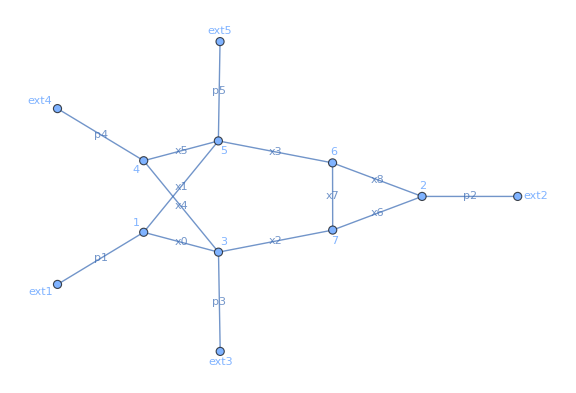

```mathematica
drawGraphFromPySecDecInput[ThreeLoopVertexInternalLines,seedExternalLines]
```

```mathematica
YaoPoly=(1-z)*(x2*(x6+x7+x8)+x6*x7)+(x3*(x6+x7+x8)+x7*x8)
Simplify[ProgramPoly+%]
```

x7 x8+x3 (x6+x7+x8)+(x6 x7+x2 (x6+x7+x8)) (1-z)

0